```mathematica
SetDirectory[NotebookDirectory[]]
PacletDirectoryAdd[{"/Users/ianfan/Downloads/WolframSummerSchoolRL-master"}];
<<WolframSummerSchoolRL`;
PacletDirectoryAdd[{"/Users/ianfan/Downloads/neuralnetworks"}]
<<NeuralNetworks`
Lookup[PacletInformation@"NeuralNetworks","Version"]
Get["RLproject-pong-q-duo.wl"]
Get["/Users/ianfan/Documents/gym-http-api/binding-wl/gym_http_client.wl"];
```

/Users/ianfan/Documents/gym-http-api/binding-wl

{/Users/ianfan/Downloads/WolframSummerSchoolRL-master,/Users/ianfan/Downloads/neuralnetworks}

11.3.7

## Nets

```mathematica
policyNet=NetInitialize@NetChain[{LinearLayer[128],Tanh,LinearLayer[128],Tanh,LinearLayer[2]},"Input"->8,"Output"->NetDecoder[{"Class",{0,1}}]];
data = preprocess[game[10,10000,policyNet,True,0,$env]];
Length[data["reward"]]
```

1709

86

## Training

```mathematica
$env=RLEnvironmentCreate["WLCartPole"]
```

RLEnvironment[…]

```mathematica
net = Import["8k-net.wlnet"]
```

NetChain[<>]

```mathematica
trained = NetTrain[policyNet, generator,LossFunction->MeanSquaredLossLayer[],BatchSize->32,MaxTrainingRounds->1000]
quitEnv[]
```

NetChain[<>]

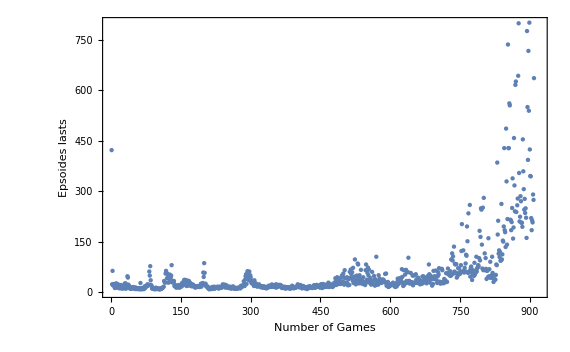

```mathematica
$rewardList;
ListPlot[$rewardList,PlotRange->800,Frame->True, FrameLabel->{"Number of Games","Epsoides lasts"}]
```

```mathematica
RLEnvironmentClose[$env]
```

```mathematica
bN = getBest[];
data = preprocess[game[1,10000,bN,True,0,$env]];
Length[data["action"]]
```

10000

```mathematica
data = preprocess[game[10,10000,net,True,0,$env]];
Length[data["action"]]
```

1

```mathematica
preprocess[game["Pong-ram-v0",10,10000,policyNet,True,0]]
```

<|action→{3,3,3,3,3,3,3,3,3,3,3,3,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,3,3,3,3,728,3,3,3,3,3,3,4,3,3,3,3,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3},2,1|>
 |  |  |  |

```mathematica
data =generator[<|"AbsoluteBatch"->0,"BatchSize"->12,"Net"->policyNet|>];
```

NetChain::invindata1: Data supplied to port "Input" was a length-132 vector, but expected a length-8 vector.

General::stop: Further output of NetChain::invindata1 will be suppressed during this calculation.

$Aborted

```mathematica
data["Input"][[2]]
```

{0.0966691,0.,0.,0.,0.0855924,0.0191324,0.,0.00352439,0.0443067,0.00100697,0.,0.,0.0966691,0.,0.,0.0317195,0.128389,0.00201394,0.000503485,0.00151045,0.,0.0916342,0.,0.0120836,0.0644461,0.0161115,0.000503485,0.0432997,0.124361,0.0432997,0.124361,0.0432997,0.124361,0.067467,0.122347,0.123354,0.122347,0.120836,0.120836,0.121843,0.121843,0.0161115,0.0161115,0.032223,0.032223,0.032223,0.0946552,0.0327265,0.0951586,0.0750192,0.0916342,0.0835785,0.0186289,0.0186289,0.0916342,0.,0.000503485,0.,0.000503485,0.0548798,0.0845855,0.0186289,0.0186289,0.0966691,0.0966691,0.0966691,0.0966691,0.0966691,0.0966691,0.101704,0.124361,0.101704,0.124361,0.101704,0.124361,0.101704,0.124361,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0906273,0.0427962,0.0271882,0.118822,0.121843,0.0609217,0.120836,0.0966691,0.,0.,0.,0.0795506,0.0191324,0.,0.00352439,0.0432997,0.00100697,0.,0.,0.0966691,0.,0.,0.0317195,0.128389,0.00201394,0.000503485,0.00151045,0.,0.0906273,0.,0.0120836,0.0644461,0.0161115,0.000503485,0.0432997,0.124361,0.0432997,0.124361,0.0432997,0.124361,0.067467,0.122347,0.123354,0.122347,0.120836,0.120836,0.121843,0.121843,0.0161115,0.0161115,0.032223,0.032223,0.032223,0.0946552,0.0327265,0.0951586,0.0760262,0.0906273,0.0876064,0.0186289,0.0186289,0.0906273,0.,0.000503485,0.,0.000503485,0.0548798,0.0835785,0.0186289,0.0186289,0.0966691,0.0966691,0.0966691,0.0966691,0.0966691,0.0966691,0.101704,0.124361,0.101704,0.124361,0.101704,0.124361,0.101704,0.124361,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0906273,0.0427962,0.0271882,0.118822,0.121843,0.0609217,0.120836}

```mathematica
Length[data["Input"]]
```

12

```mathematica
x
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
game["Pong-ram-v0",1,10,policyNet,True,0]
```

```mathematica
Quit
```

```mathematica
re = {};

ob = RLEnvironmentReset[$env];
pre = ob;
Do[
pre = Join[ob,pre];
action = net[pre];
pre = ob;
state = RLEnvironmentStep[$env, action, True];
ob = state["Observation"];
AppendTo[re,state["Rendering"]];
If[state["Done"],Break[]];
,{step,10000}];
```

```mathematica
ListAnimate[re[[;;500]],120]
```